```mathematica
u[k_]:=UnitStep[k]
```

```mathematica
v=Vo ⅇ^(- α k) u[k];
ZTransform[v,k,z]
```

(ⅇ^α Vo z)/(-1+ⅇ^α z)

(3 z)/(-1+3 z)&&S/A radio de convergencia en z

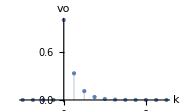

```mathematica
v1=(1/3)^k u[k];
ZTransform[v1,k,z] &&  "S/A radio de convergencia en z"
list1=Table[{k,v1},{k,-4,10,1.}];
ListPlot[list1,AxesLabel->{"k","vo"},Filling->Axis,ImageSize->Small,PlotStyle->PointSize[Medium],PlotRange->All]
```

0

-z/(-2+z)&&S/A radio de convergencia en z

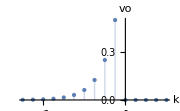

```mathematica
v2=(1/2)^-k u[-k-1];
ZTransform[v2,k,z]
∑_(k=-∞)^-1 (1/2)^-k(z)^-k &&  "S/A radio de convergencia en z"
list1=Table[{k,v2},{k,-10,4,1.}];
ListPlot[list1,AxesLabel->{"k","vo"},Filling->Axis,ImageSize->Small,PlotStyle->PointSize[Medium],PlotRange->All]
```

Cuál es ZTransform[v,k,z]&&S/A radio de convergencia en z

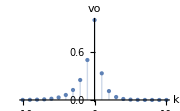

```mathematica
v=(1/2)^-k u[-k-1]+(1/3)^k u[k];
" Cuál es ZTransform[v,k,z]" &&  "S/A radio de convergencia en z"
list1=Table[{k,v},{k,-10,10,1.}];
ListPlot[list1,AxesLabel->{"k","vo"},Filling->Axis,ImageSize->Small,PlotStyle->PointSize[Medium],PlotRange->All]
```

```mathematica
Propiedades de desplazamiento y su transformada Z
```

```mathematica
ZTransform[v[k+1],k,z]
```

-z v[0]+z ZTransform[v[k],k,z]

```mathematica
ZTransform[v[k-1],k,z]
```

v[-1]+ZTransform[v[k],k,z]/z

```mathematica
Teoremas del valor inicial y final
```

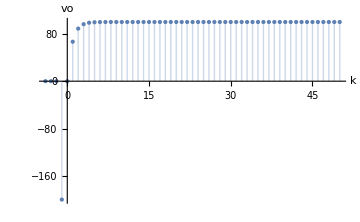

```mathematica
g[k_]:=100(1-3^-k)UnitStep[k+1]
list1=Table[{k,g[k]},{k,-4,50,1.}];
ListPlot[list1,AxesLabel->{"k","vo"},Filling->Axis,ImageSize->Medium,PlotStyle->PointSize[Medium],PlotRange->All]
```

```mathematica
APLICACIONES
```

ECUACIONES DE DIFERENCIA

```mathematica
Sol=RSolve[{v[n+1]-4 v[n-1]==0,v[-1]==2,v[0]==0},v[n],n]
```

{{v[n]→-2^(1+n) (-1+(-1)^n)}}

```mathematica
v[n_]:=2^(1+n)-(-1)^n 2^(1+n)
Lista=Table[{n,v[n]},{n,-2,3}];
ListPlot[Lista,Filling->Axis]
```

RESPUESTA DE REDES

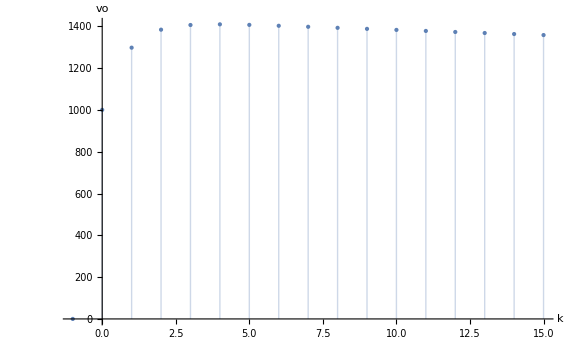

```mathematica
Clear[values,v];
{r,c1}={1,0.001};
v[k_,T_,r_,c1_]:=InverseZTransform[1/(r c1)(z^2/((z-ⅇ^(-T/(r c1)))(z-ⅇ^(-3 T)))),z,k]UnitStep[k]
values=Table[N[{k,v[k,0.0012,1,0.001]}],{k,-1,15}];

ListPlot[values,AxesLabel->{"k","vo"},Filling->Axis,ImageSize->Large,PlotStyle->PointSize[Medium],PlotRange->All]
```

```mathematica
Manipulate[ListPlot[Table[N[{k,v[k,T,r,c1]}],{k,-1,15}],AxesLabel->{"k","vo"},Filling->Axis,ImageSize->Medium,PlotStyle->PointSize[Medium],PlotRange->All],{T,0.0001,0.1,0.0001},{r,0.1,100,0.1},{c1,0.0001,0.01,0.0001}]
```

```mathematica
Hallar la corriente muestreada por el condensador en circuito RLC serie.
```